# An Introduction to Mathematica

## Exercises

Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.

```mathematica
Clear[x]
f[x_]=x*ⅇ^(-x)+x*(1-x)


f[0]
f[0.1]
f[0.2]
f[0.4]
f[0.8]
```

ⅇ^-x x+(1-x) x

0

0.180484

0.323746

0.508128

0.519463

```mathematica
f[x_]=x*ⅇ^(-x)+x*(1-x) // TeXForm
```

e^{-x} x+(1-x) x

Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

BesselJ[1,x]

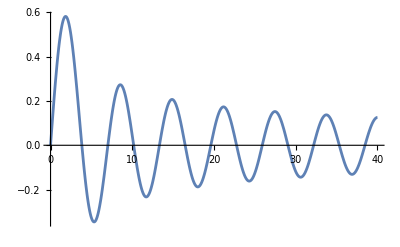

```mathematica
Clear[x]
g[x_]=BesselJ[1,x]
Plot[g[x],{x,0,40}]
```

```mathematica
FindRoot[g[x]==0,{x,0}]
```

{x→0.}

```mathematica
FindRoot[g[x]==0,{x,3}]
```

{x→3.83171}

```mathematica
FindRoot[g[x]==0,{x,6}]
```

{x→7.01559}

```mathematica
?FindRoot
```

Q3: Integrate the expression f(x) = sin(x) e^-x, and then take it’s derivative.

```mathematica
Clear[x]
f[x_]=Sin[x]*ⅇ^(-x)
myDer=D[f[x],x]
```

ⅇ^-x Sin[x]

ⅇ^-x Cos[x]-ⅇ^-x Sin[x]

```mathematica
Integrate[myDer,x]
```

ⅇ^-x Sin[x]

Q4: Find the series expansion of the function f(x) = e^(-arctan(x)) about x=0, and about x → ∞. Hint: The arctan function is ArcTan[x].

```mathematica
Clear[x]
Clear[f]
f[x_]=Exp[-ArcTan[x]]
```

ⅇ^(-ArcTan[x])

```mathematica
Series[f[x], {x,0,4}]
```

1-x+x^2/2+x^3/6-(7 x^4)/24+O[x]^5

```mathematica
Series[f[x], {x,∞,4}]
```

ⅇ^(-π/2)+ⅇ^(-π/2)/x+ⅇ^(-π/2)/(2 x^2)-ⅇ^(-π/2)/(6 x^3)-(7 ⅇ^(-π/2))/(24 x^4)+O[1/x]^5

Q5: Solve the following differential equation using both DSolve and NDSolve (for x=-10 to x=10). Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

```mathematica
Clear[x]
firstAns=DSolve[{y''[x]-x*y[x]==0,y[0]==1, y'[0]==-3^(1/3)*Gamma[2/3]/Gamma[1/3]}, y[x],x]
```

{{y[x]→3^(2/3) AiryAi[x] Gamma[2/3]}}

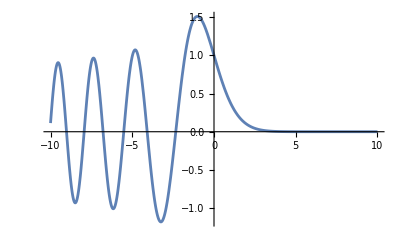

```mathematica
Plot[y[x]/.firstAns,{x,-10,10},PlotRange->Full]
```

```mathematica
secondAns=NDSolve[{y''[x]-x*y[x]==0,y[0]==1, y'[0]==-3^(1/3)*Gamma[2/3]/Gamma[1/3]}, y[x],{x,-10,10}]
```

{{y[x]→InterpolatingFunction[…][x]}}

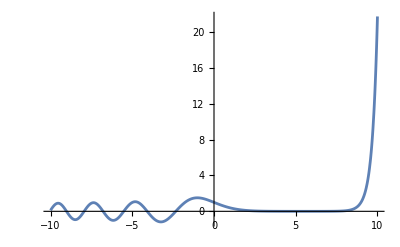

```mathematica
{{y[x]->InterpolatingFunction[…][x]}}
Plot[y[x]/.secondAns,{x,-10,10},PlotRange->Full]
```